```mathematica
ClearAll["Global`*"]
```

### CIP - BS plots; Ref: NIFS-778, Basis Set Approach in the Constrained Interpolation Profile Method, T. Utsumi, J. Koga, T. Yabe, Y. Ogata, E. Matsunaga, T. Aoki and M. Sekine, July 2003

```mathematica
θ[x_]:=HeavisideTheta[x]-HeavisideTheta[x-1]
```

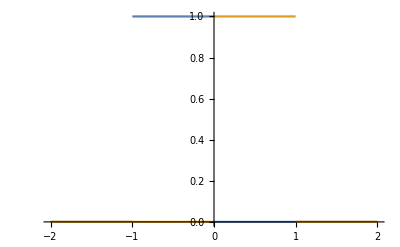

```mathematica
Plot[{θ[x+1],θ[x]},{x,-2,2}]
```

#### CIP-BS^0;

```mathematica
ϕ0m[x_,ξ_,dx_]:=1+1/dx(x-ξ)
ϕ0p[x_,ξ_,dx_]:=1-1/dx(x-ξ)
```

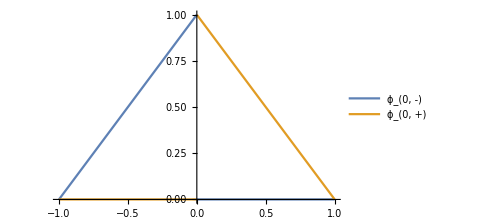

```mathematica
Plot[{ϕ0m[x,0,1]θ[x+1],ϕ0p[x,0,1]θ[x]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"ϕ_(0, -)","ϕ_(0, +)"}]
```

#### CIP-BS^1;

```mathematica
ϕ0m[x_,ξ_,dx_]:=1-3/dx^2(x-ξ)^2-2/dx^3(x-ξ)^3
ϕ0p[x_,ξ_,dx_]:=1-3/dx^2(x-ξ)^2+2/dx^3(x-ξ)^3
ϕ1m[x_,ξ_,dx_]:=x-ξ+2/dx(x-ξ)^2+1/dx^2(x-ξ)^3
ϕ1p[x_,ξ_,dx_]:=x-ξ-2/dx(x-ξ)^2+1/dx^2(x-ξ)^3
```

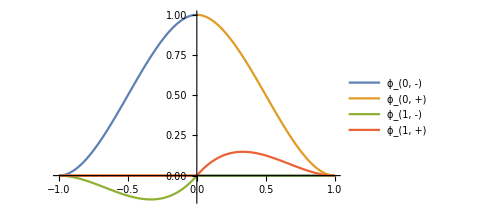

```mathematica
Plot[{ϕ0m[x,0,1]θ[x+1],ϕ0p[x,0,1]θ[x],ϕ1m[x,0,1]θ[x+1],ϕ1p[x,0,1]θ[x]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"ϕ_(0, -)","ϕ_(0, +)","ϕ_(1, -)","ϕ_(1, +)"}]
```

#### CIP-BS^2;

```mathematica
ϕ0m[x_,ξ_,dx_]:=1+10/dx^3(x-ξ)^3+15/dx^4(x-ξ)^4+6/dx^5(x-ξ)^5;
ϕ0p[x_,ξ_,dx_]:=1-10/dx^3(x-ξ)^3+15/dx^4(x-ξ)^4-6/dx^5(x-ξ)^5;
ϕ1m[x_,ξ_,dx_]:=(x-ξ)-6/dx^2(x-ξ)^3-8/dx^3(x-ξ)^4-3/dx^4(x-ξ)^5;
ϕ1p[x_,ξ_,dx_]:=(x-ξ)-6/dx^2(x-ξ)^3+8/dx^3(x-ξ)^4-3/dx^4(x-ξ)^5;
ϕ2m[x_,ξ_,dx_]:=1/2(x-ξ)^2+3/(2 dx)(x-ξ)^3+3/(2 dx^2)(x-ξ)^4+1/(2 dx^3)(x-ξ)^5;
ϕ2p[x_,ξ_,dx_]:=1/2(x-ξ)^2-3/(2 dx)(x-ξ)^3+3/(2 dx^2)(x-ξ)^4-1/(2 dx^3)(x-ξ)^5;
```

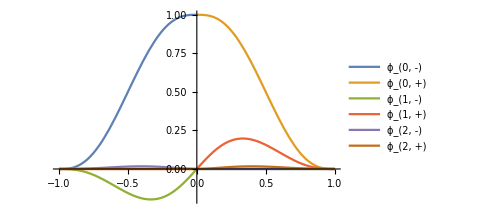

```mathematica
Plot[{ϕ0m[x,0,1]θ[x+1],ϕ0p[x,0,1]θ[x],ϕ1m[x,0,1]θ[x+1],ϕ1p[x,0,1]θ[x],ϕ2m[x,0,1]θ[x+1],ϕ2p[x,0,1]θ[x]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"ϕ_(0, -)","ϕ_(0, +)","ϕ_(1, -)","ϕ_(1, +)","ϕ_(2, -)","ϕ_(2, +)"}]
```

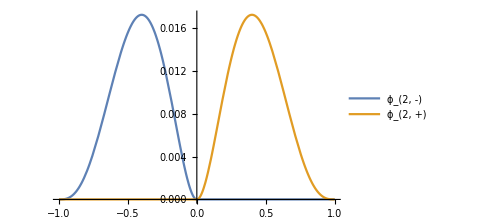

```mathematica
Plot[{ϕ2m[x,0,1]θ[x+1],ϕ2p[x,0,1]θ[x]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"ϕ_(2, -)","ϕ_(2, +)"}]
```

```mathematica
FTup[t_]:=Product[Sinc[t 2^-n],{n,1,5}]
up[x_]:=If[Abs[x]≤1,0.5+Sum[FTup[k π]Cos[k π x],{k,1,30}],0]
B3[x_]:=BSplineBasis[3,1/2(x+1)]
```

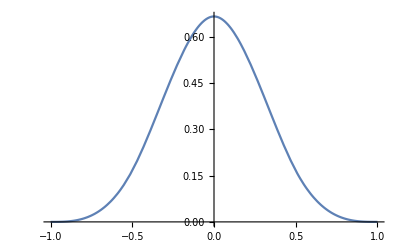

```mathematica
Plot[B3[x],{x,-1,1}]
```

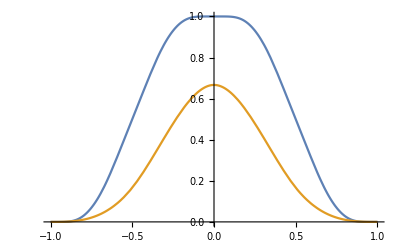

```mathematica
Plot[{up[x],B3[x]},{x,-1,1}]
```

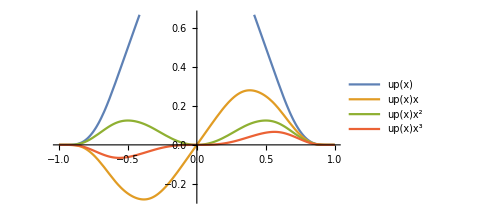

```mathematica
Plot[{up[x],up[x]x,up[x] x^2,up[x] x^3},{x,-1,1},PlotLegends->{"up(x)","up(x)x","up(x)x^2","up(x)x^3"},ImageSize->Medium]
```

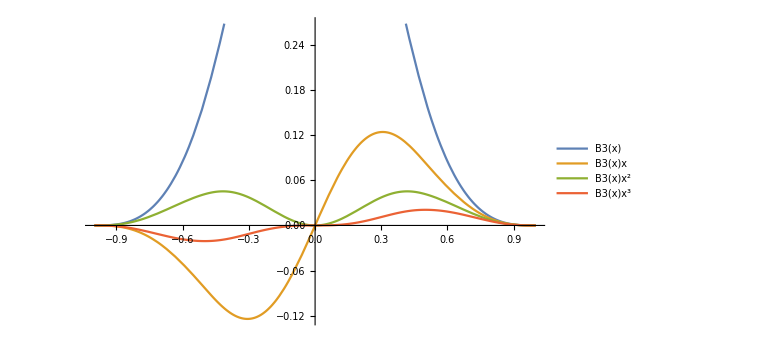

```mathematica
Plot[{B3[x],B3[x]x,B3[x] x^2,B3[x] x^3},{x,-1,1},PlotLegends->{"B3(x)","B3(x)x","B3(x)x^2","B3(x)x^3"},ImageSize->Large]
```

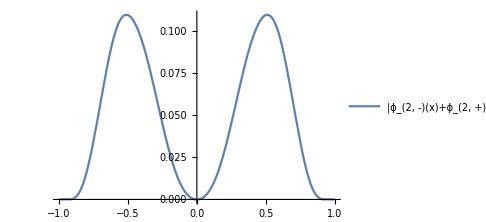

```mathematica
Plot[{Abs[ϕ2m[x,0,1]θ[x+1]+ϕ2p[x,0,1]θ[x]-up[x] x^2]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"|ϕ_(2, -)(x)+ϕ_(2, +)(x)-up(x)x^2|"}]
```

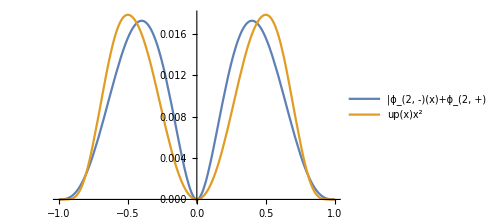

```mathematica
Plot[{ϕ2m[x,0,1]θ[x+1]+ϕ2p[x,0,1]θ[x],1/7 up[x] x^2},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"|ϕ_(2, -)(x)+ϕ_(2, +)(x)","up(x)x^2"}]
```

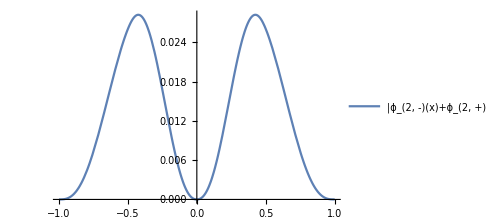

```mathematica
Plot[{Abs[ϕ2m[x,0,1]θ[x+1]+ϕ2p[x,0,1]θ[x]-B3[x] x^2]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"|ϕ_(2, -)(x)+ϕ_(2, +)(x)-up(x)x^2|"}]
```

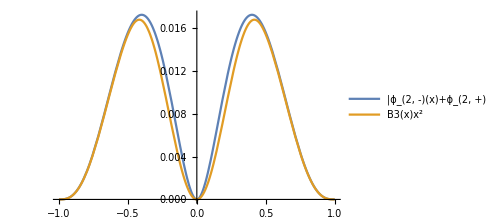

```mathematica
Plot[{ϕ2m[x,0,1]θ[x+1]+ϕ2p[x,0,1]θ[x],1/2.7 B3[x] x^2},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"|ϕ_(2, -)(x)+ϕ_(2, +)(x)","B3(x)x^2"}]
```

## CIP-BS^0;

```mathematica
ϕ0[x_]:=a+b x
```

### Constrains;

```mathematica
EqnSys={
ϕ0[-h]==0,
ϕ0[0]==1
};
SolEqnSys=Solve[EqnSys,{a,b}];
ϕ0[x]/.Flatten[SolEqnSys]
EqnSys={
ϕ0[h]==0,
ϕ0[0]==1
};
SolEqnSys=Solve[EqnSys,{a,b}];
ϕ0[x]/.Flatten[SolEqnSys]
```

1+x/h

1-x/h

### Comparison with cubic B - spline;

```mathematica
ϕ0[x_]:=BSplineBasis[3,1/4(x+2)];
ϕ1[x_]:=1/4 (4 BSplineBasis[2,0,(2+x)/3]-4 BSplineBasis[2,1,(2+x)/3]);
ϕ2[x_]:=1/4 (4/3 (3 BSplineBasis[1,0,(2+x)/2]-3 BSplineBasis[1,1,(2+x)/2])-4/3 (3 BSplineBasis[1,1,(2+x)/2]-3 BSplineBasis[1,2,(2+x)/2]));
{{ϕ0[-1],ϕ0[0],ϕ0[1]},
{ϕ1[-1],ϕ1[0],ϕ1[1]},
{ϕ2[-1],ϕ2[0],ϕ2[1]}}//Grid
```

1/6 | 2/3 | 1/6
1/2 | 0 | -1/2
1 | -2 | 1

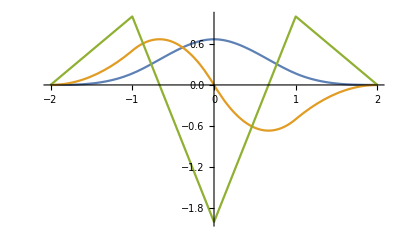

```mathematica
Plot[{ϕ0[x],ϕ1[x],ϕ2[x]},{x,-2,2}]
```

## CIP-BS^1;

```mathematica
ϕl[x_]:=a+b x +c x^2 +d x^3
```

### Constrains;

```mathematica
EqnSys={
Table[(D[ϕl[x],{x,k}]/.x->-h)==0,{k,0,1}],
(D[ϕl[x],{x,0}]/.x->  0)==1,
(D[ϕl[x],{x,1}]/.x->  0)==0
}//Flatten;
SolEqnSys=Solve[EqnSys,{a,b,c,d}];

ϕl[x]/.Flatten[SolEqnSys]
EqnSys={
Table[(D[ϕl[x],{x,k}]/.x->h)==0,{k,0,1}],
(D[ϕl[x],{x,0}]/.x->0)==1,
(D[ϕl[x],{x,1}]/.x->0)==0
}//Flatten;
SolEqnSys=Solve[EqnSys,{a,b,c,d}];
ϕl[x]/.Flatten[SolEqnSys]
```

1-(3 x^2)/h^2-(2 x^3)/h^3

1-(3 x^2)/h^2+(2 x^3)/h^3

```mathematica
EqnSys={
Table[(D[ϕl[x],{x,k}]/.x->-h)==0,{k,0,1}],
ϕl[0]==0,
(D[ϕl[x],x]/.x->0)==1
}//Flatten;
SolEqnSys=Solve[EqnSys,{a,b,c,d}];
ϕl[x]/.Flatten[SolEqnSys]
EqnSys={
Table[(D[ϕl[x],{x,k}]/.x->h)==0,{k,0,1}],
ϕl[0]==0,
(D[ϕl[x],x]/.x->0)==1
}//Flatten;
SolEqnSys=Solve[EqnSys,{a,b,c,d}];
ϕl[x]/.Flatten[SolEqnSys]
```

x+(2 x^2)/h+x^3/h^2

x-(2 x^2)/h+x^3/h^2

## CIP-BS^2;

```mathematica
ϕ2[x_]:=a+b x +c x^2 +d x^3+e x^4+f x^5
```

### Constrains;

```mathematica
EqnSys={
Table[(D[ϕ2[x],{x,k}]/.x->-h)==0,{k,0,2}],
(D[ϕ2[x],{x,0}]/.x->0)==1,
Table[(D[ϕ2[x],{x,k}]/.x->0)==0,{k,1,2}]
}//Flatten;
SolEqnSys=Solve[EqnSys,{a,b,c,d,e,f}];
ϕ2[x]/.Flatten[SolEqnSys]
EqnSys={
Table[(D[ϕ2[x],{x,k}]/.x->h)==0,{k,0,2}],
(D[ϕ2[x],{x,0}]/.x->0)==1,
Table[(D[ϕ2[x],{x,k}]/.x->0)==0,{k,1,2}]
}//Flatten;
SolEqnSys=Solve[EqnSys,{a,b,c,d,e,f}];

ϕ2[x]/.Flatten[SolEqnSys]
EqnSys={
ϕ2[-h]==0,
ϕ2[0]==0,
(D[ϕ2[x],x]/.x->-h)==0,
(D[ϕ2[x],x]/.x->0)==1,
(D[ϕ2[x],{x,2}]/.x->-h)==0,
(D[ϕ2[x],{x,2}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a,b,c,d,e,f}];
ϕ2[x]/.Flatten[SolEqnSys]
EqnSys={
ϕ2[h]==0,
ϕ2[0]==0,
(D[ϕ2[x],x]/.x->h)==0,
(D[ϕ2[x],x]/.x->0)==1,
(D[ϕ2[x],{x,2}]/.x->h)==0,
(D[ϕ2[x],{x,2}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a,b,c,d,e,f}];
ϕ2[x]/.Flatten[SolEqnSys]

EqnSys={
ϕ2[-h]==0,
ϕ2[0]==0,
(D[ϕ2[x],x]/.x->-h)==0,
(D[ϕ2[x],x]/.x->0)==0,
(D[ϕ2[x],{x,2}]/.x->-h)==0,
(D[ϕ2[x],{x,2}]/.x->0)==1
};
SolEqnSys=Solve[EqnSys,{a,b,c,d,e,f}];
ϕ2[x]/.Flatten[SolEqnSys]
EqnSys={
ϕ2[h]==0,
ϕ2[0]==0,
(D[ϕ2[x],x]/.x->h)==0,
(D[ϕ2[x],x]/.x->0)==0,
(D[ϕ2[x],{x,2}]/.x->h)==0,
(D[ϕ2[x],{x,2}]/.x->0)==1
};
SolEqnSys=Solve[EqnSys,{a,b,c,d,e,f}];
ϕ2[x]/.Flatten[SolEqnSys]
```

1+(10 x^3)/h^3+(15 x^4)/h^4+(6 x^5)/h^5

1-(10 x^3)/h^3+(15 x^4)/h^4-(6 x^5)/h^5

x-(6 x^3)/h^2-(8 x^4)/h^3-(3 x^5)/h^4

x-(6 x^3)/h^2+(8 x^4)/h^3-(3 x^5)/h^4

x^2/2+(3 x^3)/(2 h)+(3 x^4)/(2 h^2)+x^5/(2 h^3)

x^2/2-(3 x^3)/(2 h)+(3 x^4)/(2 h^2)-x^5/(2 h^3)

## CIP-BS^3;

```mathematica
Clear[a,b,c,d,e,f]
```

```mathematica
ϕ3[x_]:=a0+a1 x +a2 x^2 +a3 x^3+a4 x^4+a5 x^5+a6 x^6+a7 x^7
```

### Constrains;

```mathematica
EqnSys={
(D[ϕ3[x],{x,0}]/.x->-h)==0,
(D[ϕ3[x],{x,0}]/.x->0)==1,
(D[ϕ3[x],{x,1}]/.x->-h)==0,
(D[ϕ3[x],{x,1}]/.x->0)==0,
(D[ϕ3[x],{x,2}]/.x->-h)==0,
(D[ϕ3[x],{x,2}]/.x->0)==0,
(D[ϕ3[x],{x,3}]/.x->-h)==0,
(D[ϕ3[x],{x,3}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7}];
ϕ30l=ϕ3[x]/.Flatten[SolEqnSys]/.h->1
EqnSys={
ϕ3[h]==0,
ϕ3[0]==1,
(D[ϕ3[x],{x,1}]/.x->h)==0,
(D[ϕ3[x],{x,1}]/.x->0)==0,
(D[ϕ3[x],{x,2}]/.x->h)==0,
(D[ϕ3[x],{x,2}]/.x->0)==0,
(D[ϕ3[x],{x,3}]/.x->h)==0,
(D[ϕ3[x],{x,3}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7}];
ϕ30r=ϕ3[x]/.Flatten[SolEqnSys]/.h->1

EqnSys={
ϕ3[-h]==0,
ϕ3[0]==0,
(D[ϕ3[x],x]/.x->-h)==0,
(D[ϕ3[x],x]/.x->0)==1,
(D[ϕ3[x],{x,2}]/.x->-h)==0,
(D[ϕ3[x],{x,2}]/.x->0)==0,
(D[ϕ3[x],{x,3}]/.x->-h)==0,
(D[ϕ3[x],{x,3}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7}];
ϕ31l=ϕ3[x]/.Flatten[SolEqnSys]/.h->1
EqnSys={
ϕ3[h]==0,
ϕ3[0]==0,
(D[ϕ3[x],x]/.x->h)==0,
(D[ϕ3[x],x]/.x->0)==1,
(D[ϕ3[x],{x,2}]/.x->h)==0,
(D[ϕ3[x],{x,2}]/.x->0)==0,
(D[ϕ3[x],{x,3}]/.x->h)==0,
(D[ϕ3[x],{x,3}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7}];
ϕ31r=ϕ3[x]/.Flatten[SolEqnSys]/.h->1

EqnSys={
ϕ3[-h]==0,
ϕ3[0]==0,
(D[ϕ3[x],x]/.x->-h)==0,
(D[ϕ3[x],x]/.x->0)==0,
(D[ϕ3[x],{x,2}]/.x->-h)==0,
(D[ϕ3[x],{x,2}]/.x->0)==1,
(D[ϕ3[x],{x,3}]/.x->-h)==0,
(D[ϕ3[x],{x,3}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7}];
ϕ32l=ϕ3[x]/.Flatten[SolEqnSys]/.h->1
EqnSys={
ϕ3[h]==0,
ϕ3[0]==0,
(D[ϕ3[x],x]/.x->h)==0,
(D[ϕ3[x],x]/.x->0)==0,
(D[ϕ3[x],{x,2}]/.x->h)==0,
(D[ϕ3[x],{x,2}]/.x->0)==1,
(D[ϕ3[x],{x,3}]/.x->h)==0,
(D[ϕ3[x],{x,3}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7}];
ϕ32r=ϕ3[x]/.Flatten[SolEqnSys]/.h->1

EqnSys={
ϕ3[-h]==0,
ϕ3[0]==0,
(D[ϕ3[x],x]/.x->-h)==0,
(D[ϕ3[x],x]/.x->0)==0,
(D[ϕ3[x],{x,2}]/.x->-h)==0,
(D[ϕ3[x],{x,2}]/.x->0)==0,
(D[ϕ3[x],{x,3}]/.x->-h)==0,
(D[ϕ3[x],{x,3}]/.x->0)==1
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7}];
ϕ33l=ϕ3[x]/.Flatten[SolEqnSys]/.h->1
EqnSys={
ϕ3[h]==0,
ϕ3[0]==0,
(D[ϕ3[x],x]/.x->h)==0,
(D[ϕ3[x],x]/.x->0)==0,
(D[ϕ3[x],{x,2}]/.x->h)==0,
(D[ϕ3[x],{x,2}]/.x->0)==0,
(D[ϕ3[x],{x,3}]/.x->h)==0,
(D[ϕ3[x],{x,3}]/.x->0)==1
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7}];
ϕ33r=ϕ3[x]/.Flatten[SolEqnSys]/.h->1
```

1-35 x^4-84 x^5-70 x^6-20 x^7

1-35 x^4+84 x^5-70 x^6+20 x^7

x+20 x^4+45 x^5+36 x^6+10 x^7

x-20 x^4+45 x^5-36 x^6+10 x^7

x^2/2-5 x^4-10 x^5-(15 x^6)/2-2 x^7

x^2/2-5 x^4+10 x^5-(15 x^6)/2+2 x^7

x^3/6+(2 x^4)/3+x^5+(2 x^6)/3+x^7/6

x^3/6-(2 x^4)/3+x^5-(2 x^6)/3+x^7/6

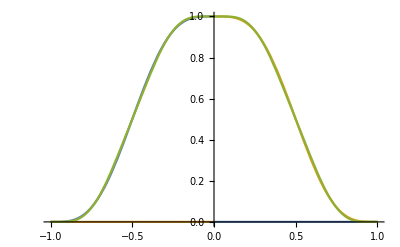

```mathematica
Plot[{θ[x+1]ϕ30l,θ[x]ϕ30r,up[x]},{x,-1,1}]
```

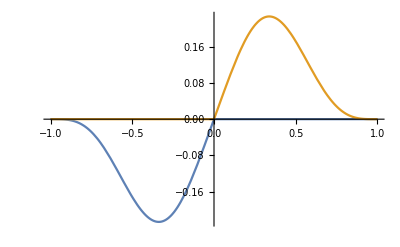

```mathematica
Plot[{θ[x+1]ϕ31l,θ[x]ϕ31r},{x,-1,1},PlotRange->Full]
```

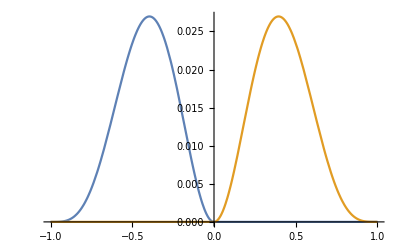

```mathematica
Plot[{θ[x+1]ϕ32l,θ[x]ϕ32r},{x,-1,1},PlotRange->Full]
```

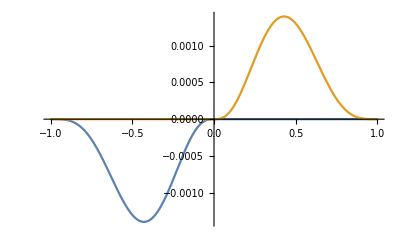

```mathematica
Plot[{θ[x+1]ϕ33l,θ[x]ϕ33r},{x,-1,1},PlotRange->Full]
```

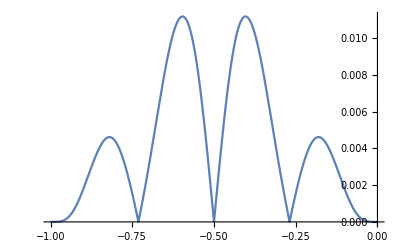

```mathematica
Plot[{Abs[θ[x+1]ϕ30l-up[x]]},{x,-1,0}]
```

## CIP-BS^4;

```mathematica
ϕ4[x_]:=a0+a1 x +a2 x^2 +a3 x^3+a4 x^4+a5 x^5+a6 x^6+a7 x^7+a8 x^8+a9 x^9
```

```mathematica
EqnSys={
(D[ϕ4[x],{x,0}]/.x->-h)==0,
(D[ϕ4[x],{x,0}]/.x->0)==1,
(D[ϕ4[x],{x,1}]/.x->-h)==0,
(D[ϕ4[x],{x,1}]/.x->0)==0,
(D[ϕ4[x],{x,2}]/.x->-h)==0,
(D[ϕ4[x],{x,2}]/.x->0)==0,
(D[ϕ4[x],{x,3}]/.x->-h)==0,
(D[ϕ4[x],{x,3}]/.x->0)==0,
(D[ϕ4[x],{x,4}]/.x->-h)==0,
(D[ϕ4[x],{x,4}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7,a8,a9}];
ϕ40l=ϕ4[x]/.Flatten[SolEqnSys]/.h->1
EqnSys={
(D[ϕ4[x],{x,0}]/.x->h)==0,
(D[ϕ4[x],{x,0}]/.x->0)==1,
(D[ϕ4[x],{x,1}]/.x->h)==0,
(D[ϕ4[x],{x,1}]/.x->0)==0,
(D[ϕ4[x],{x,2}]/.x->h)==0,
(D[ϕ4[x],{x,2}]/.x->0)==0,
(D[ϕ4[x],{x,3}]/.x->h)==0,
(D[ϕ4[x],{x,3}]/.x->0)==0,
(D[ϕ4[x],{x,4}]/.x->h)==0,
(D[ϕ4[x],{x,4}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7,a8,a9}];
ϕ40r=ϕ4[x]/.Flatten[SolEqnSys]/.h->1
```

1+126 x^5+420 x^6+540 x^7+315 x^8+70 x^9

1-126 x^5+420 x^6-540 x^7+315 x^8-70 x^9

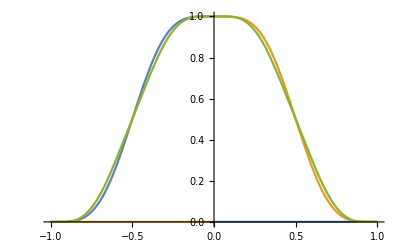

```mathematica
Plot[{θ[x+1]ϕ40l,θ[x]ϕ40r,up[x]},{x,-1,1}]
```

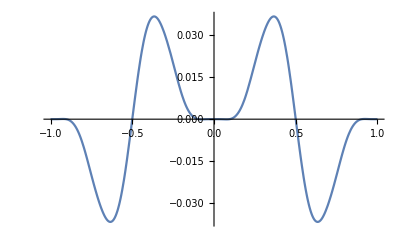

```mathematica
Plot[{θ[x+1]ϕ40l+θ[x]ϕ40r-up[x]},{x,-1,1}]
```

## CIP-BS^5;

```mathematica
ϕ5[x_]:=a0+a1 x +a2 x^2 +a3 x^3+a4 x^4+a5 x^5+a6 x^6+a7 x^7+a8 x^8+a9 x^9+a10 x^10+a11 x^11
```

```mathematica
EqnSys={
(D[ϕ5[x],{x,0}]/.x->-h)==0,
(D[ϕ5[x],{x,0}]/.x->0)==1,
(D[ϕ5[x],{x,1}]/.x->-h)==0,
(D[ϕ5[x],{x,1}]/.x->0)==0,
(D[ϕ5[x],{x,2}]/.x->-h)==0,
(D[ϕ5[x],{x,2}]/.x->0)==0,
(D[ϕ5[x],{x,3}]/.x->-h)==0,
(D[ϕ5[x],{x,3}]/.x->0)==0,
(D[ϕ5[x],{x,4}]/.x->-h)==0,
(D[ϕ5[x],{x,4}]/.x->0)==0,
(D[ϕ5[x],{x,5}]/.x->-h)==0,
(D[ϕ5[x],{x,5}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11}];
ϕ50l=ϕ5[x]/.Flatten[SolEqnSys]/.h->1
EqnSys={
(D[ϕ5[x],{x,0}]/.x->h)==0,
(D[ϕ5[x],{x,0}]/.x->0)==1,
(D[ϕ5[x],{x,1}]/.x->h)==0,
(D[ϕ5[x],{x,1}]/.x->0)==0,
(D[ϕ5[x],{x,2}]/.x->h)==0,
(D[ϕ5[x],{x,2}]/.x->0)==0,
(D[ϕ5[x],{x,3}]/.x->h)==0,
(D[ϕ5[x],{x,3}]/.x->0)==0,
(D[ϕ5[x],{x,4}]/.x->h)==0,
(D[ϕ5[x],{x,4}]/.x->0)==0,
(D[ϕ5[x],{x,5}]/.x->h)==0,
(D[ϕ5[x],{x,5}]/.x->0)==0
};
SolEqnSys=Solve[EqnSys,{a0,a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11}];
ϕ50r=ϕ5[x]/.Flatten[SolEqnSys]/.h->1
```

1-462 x^6-1980 x^7-3465 x^8-3080 x^9-1386 x^10-252 x^11

1-462 x^6+1980 x^7-3465 x^8+3080 x^9-1386 x^10+252 x^11

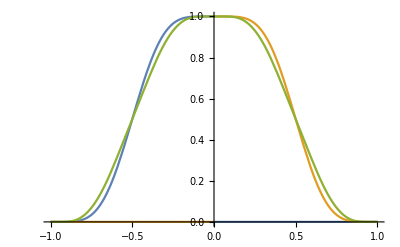

```mathematica
Plot[{θ[x+1]ϕ50l,θ[x]ϕ50r,up[x]},{x,-1,1}]
```

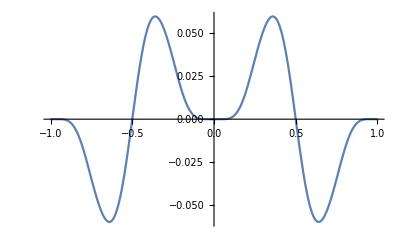

```mathematica
Plot[{θ[x+1]ϕ50l+θ[x]ϕ50r-up[x]},{x,-1,1}]
```